# PS05 Problem 4 on Einstein solid

```mathematica
CoverNk[t_]:= Exp[1/t]/(Exp[1/t]-1)^2/t^2
```

Plot only from t = 0.01 to avoid error message.

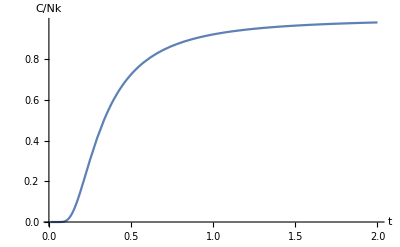

```mathematica
Plot[CoverNk[t],{t,0.01,2},AxesLabel->{t,C/Nk}]
```

To do part (f), just expand the heat capacity CoverNk[t] about t = Infinity up to 2 terms:

```mathematica
s1 = Series[CoverNk[t],{t,Infinity,2}]
```

1-1/(12 t^2)+O[1/t]^3

```mathematica
CoverNkapprox[t_]= Normal[s1]
```

1-1/(12 t^2)

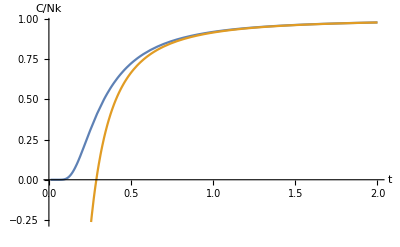

```mathematica
Plot[{CoverNk[t],CoverNkapprox[t]},{t,0.01,2},AxesLabel->{t,C/Nk}]
```